# Kim Optimization Procedure

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

# P4 Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=3; (*Number of free parameters*)
nX=2; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,β};
freePars={a1,a2,a3};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Kim's integrand, Δ^2=(κ-N/D)^2*)
ΔKim22024[κ_]=(κ-Num[κ]/Denom[κ])^2//Together//TrigReduce;
ΔKim2[κ_]=((1+δ)*κ*Denom[κ]-Num[κ])^2*(κ/r)^n;

(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
(*EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<1,n∈Integers,δ∈Reals}];*)
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
```

```mathematica
EDHConstr=EDH/.Solve[{fixedEq1,fixedEq2},{fixedPars[[1]],fixedPars[[2]]}][[1]];

(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDHConstr,freePars[[1]]]==0;
freeEq2=D[EDHConstr,freePars[[2]]]==0;
freeEq3=D[EDHConstr,freePars[[3]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
coeffs//TableForm

freeEq1=D[EKim,freePars[[1]]]==0;
freeEq2=D[EKim,freePars[[2]]]==0;
freeEq3=D[EKim,freePars[[3]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]]
N[coeffs,15]//TableForm
```

{α→0.577046,β→0.0890084,a1→0.651708,a2→0.248159,a3→0.00600963}

α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963

{α→0.580326-3.30734×10^-17 ⅈ,β→0.0912657-2.32526×10^-17 ⅈ,a1→0.648644+3.06003×10^-17 ⅈ,a2→0.251901-3.73485×10^-17 ⅈ,a3→0.00638218-4.07645×10^-18 ⅈ}

α→0.580326-3.30734×10^-17 ⅈ
β→0.0912657-2.32526×10^-17 ⅈ
a1→0.648644+3.06003×10^-17 ⅈ
a2→0.251901-3.73485×10^-17 ⅈ
a3→0.00638218-4.07645×10^-18 ⅈ

## Results

Optimizing over α, β, and a_1 (with r=2.661/π):
	Our results:
		α→0.567498
β→0.0827093
a1→0.660388
a2→0.237376
a3→0.0050227
	Kim’s results:
		α->0.5856396845642288
β->0.09505833117193530
a_1->0.6437151795729501
a_2->0.2578941677285964
a_3->0.007064833568673624

Optimizing over α, β and a_2 (with r=2.671/π):
	Our results:
		α→0.569865
β→0.0842237
a1→0.658279
a2→0.240028
a3→0.00525085
	Kim’s results:
		α->0.5859572811123209
β->0.09527180900906593
a_1->0.6434288190645918
a_2->0.2582497707129994
a_3->0.007100243210265430

Optimizing over β, a_2, and a_3 (with r=2.669/π):
	Our results:
		α→0.462125
β→0.0143368
a1→0.754521
a2→0.119357
a3→-0.00559121
	Kim’s results:
		α->0.5864696980962217
β->0.09564623994911990
a_1->0.6429512471438849
a_2->0.2588269491578893
a_3->0.007170264195226098

Optimizing over α, β, and a_3 (with r=2.672/π):
	Our results:
		α→0.584338
β→0.0937535
a1→0.645146
a2→0.25636
a3→0.00674177
	Kim’s results:
		α->0.5862704032801503
β->0.09549533555017055
a_1->0.6431406736919156
a_2->0.2586011023495066
a_3->0.007140953479797375


Correct results (r=2.670):
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963
	α→0.577046
β→0.0890084
a1→0.651708
a2→0.248159
a3→0.00600963

## Visualization

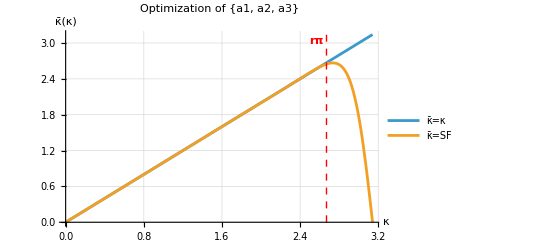

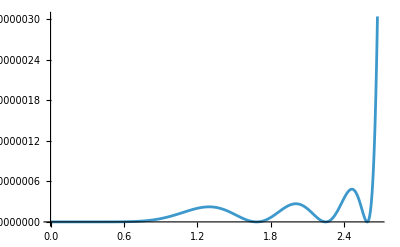

```mathematica
coeffs1={α->0.5674984766667983,β->0.08270928003870921,a1->0.6603882207694884,a2->0.23737572537287543,a3->0.005022695063422676};
r1=2.661/π;
coeffs2={α->0.5698649252859338,β->0.08422366118619422,a1->0.6582794461943285,a2->0.24002829986023835,a3->0.005250846852440635};
r2=2.671/π;
coeffs3={α->0.46212528854158036,β->0.01433680907756551,a1->0.7545208706724549,a2->0.11935743386371474,a3->-0.0055912135935795295};
r3=2.669/π;
coeffs4={α->0.5843384783205174,β->0.09375348681411781,a1->0.6451457202668986,a2->0.2563604647345564,a3->0.00674177179954127};
r4=2.672/π;

coeffsCor={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};
rCor=2.670/π;
Plot[{κ,κBar[κ]/.coeffsCor},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π}}],Text[Style["rπ",Bold],{rCor*π-0.1,π-0.1}]}]

Plot[ΔDH2[κ]/.coeffsCor,{κ,0,r π},PlotRange->All]

(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
```

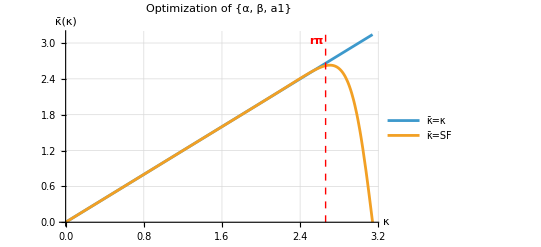

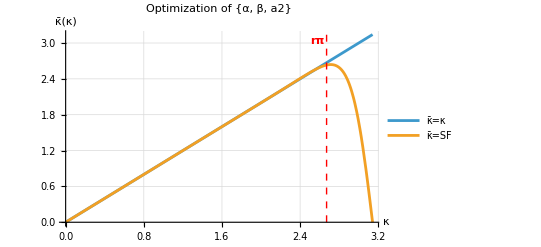

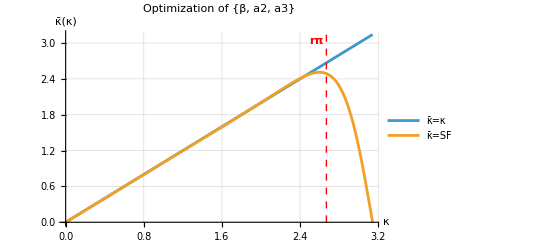

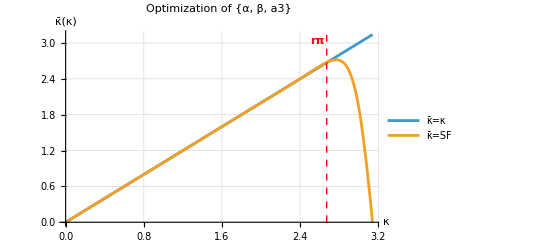

```mathematica
Plot[{κ,κBar[κ]/.coeffs1},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a1}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r1*π,0},{r1*π,π}}],Text[Style["rπ",Bold],{r1*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs2},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r2*π,0},{r2*π,π}}],Text[Style["rπ",Bold],{r2*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs3},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{β,a2,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r3*π,0},{r3*π,π}}],Text[Style["rπ",Bold],{r3*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r4*π,0},{r4*π,π}}],Text[Style["rπ",Bold],{r4*π-0.1,π-0.1}]}]
```

## Zoomed In Plots

-Graphics-

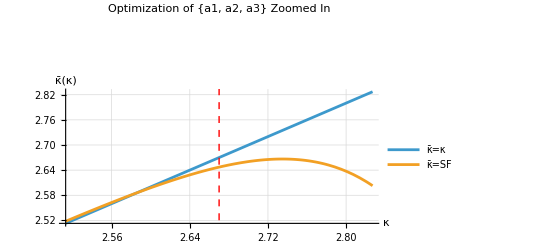

```mathematica
(*ϵ is the zoom factor; the zoomed plot will go from (r-ϵ)π to (r+ϵ)π*)
ϵ=0.05;

Plot[{κ,κBar[κ]/.coeffsCor},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π}}],Text[Style["rπ",Bold],{rCor*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffsCor},{κ,(rCor-ϵ)*π,(rCor+ϵ)*π},PlotRange->{(rCor-ϵ)*π,(rCor+ϵ)*π},PlotLabel->"Optimization of "<>ToString[freePars]<>"\nZoomed In",AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π}}],Text[Style["rπ",Bold],{rCor*π-0.05,π-0.2}]}]
```

## Varying r Values

```mathematica
ΔDH2[κ];
Clear[EDH,𝓇]
EDH[𝓇_]=Integrate[ΔDH2[κ],{κ,0,𝓇*π}]/.coeffs4
totError=EDH[1]
```

3.02836 𝓇+17.5752 𝓇^3+5.66594 𝓇 Cos[2 π 𝓇]+1.06207 𝓇 Cos[3 π 𝓇]+0.0947869 𝓇 Cos[4 π 𝓇]+0.00158855 𝓇 Cos[5 π 𝓇]+Cos[π 𝓇] (25.3004 𝓇-0.341451 Sin[π 𝓇])-7.38488 Sin[π 𝓇]+25.2315 𝓇^2 Sin[π 𝓇]-1.13855 Sin[2 π 𝓇]+5.22061 𝓇^2 Sin[2 π 𝓇]-0.333209 Sin[3 π 𝓇]+0.720926 𝓇^2 Sin[3 π 𝓇]-0.0447527 Sin[4 π 𝓇]+0.0433755 𝓇^2 Sin[4 π 𝓇]-0.00148379 Sin[5 π 𝓇]-0.0000151505 Sin[6 π 𝓇]

0.000281384

```mathematica
(*D[EDH[r4],freePars[[1]]]
D[EDH[r4],freePars[[2]]]
D[EDH[r4],freePars[[3]]]*)
```

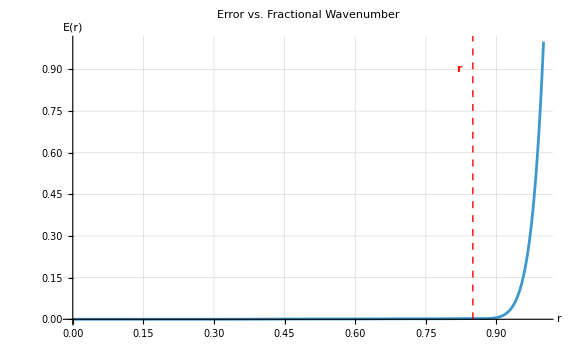

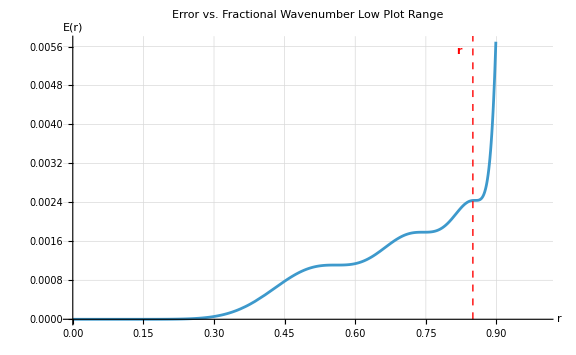

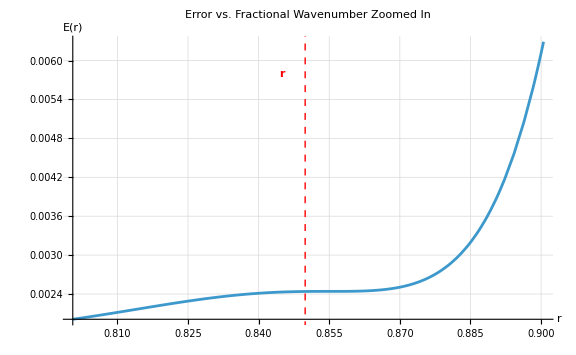

-Graphics-

-Graphics-

```mathematica
Plot[1/totError EDH[𝓇],{𝓇,0,1},PlotRange->All,PlotLabel->"Error vs. Fractional Wavenumber",AxesLabel->{"r","E(r)"},GridLines->Automatic,Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r,0},{r,1.5}}],Text[Style["r",Bold],{r-0.03,0.9}]},ImageSize->Large]
Plot[1/totError EDH[𝓇],{𝓇,0,1},PlotLabel->"Error vs. Fractional Wavenumber\nLow Plot Range",AxesLabel->{"r","E(r)"},GridLines->Automatic,Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r,0},{r,1.5}}],Text[Style["r",Bold],{r-0.03,0.0055}]},ImageSize->Large]
Plot[1/totError EDH[𝓇],{𝓇,r4-ϵ,r4+ϵ},PlotRange->All,PlotLabel->"Error vs. Fractional Wavenumber\nZoomed In",AxesLabel->{"r","E(r)"},GridLines->Automatic,Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r,0},{r,1.5}}],Text[Style["r",Bold],{r-0.005,0.0058}]},ImageSize->Large]
```

## Convergence as r->1?

```mathematica
Clear[r]
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1]
```

2 a1^2 π r+2 a2^2 π r+2 a3^2 π r+(π^3 r^3)/3+2/3 π^3 r^3 α^2+2/3 π^3 r^3 β^2+4 π r (a1-a1 β+a3 β+α (2+a2+2 β)) Cos[π r]+π r (2 a2+2 a1 α+2 a3 α+α^2+2 β) Cos[2 π r]+4/3 a3 π r Cos[3 π r]+4/3 a2 π r α Cos[3 π r]+4/3 a1 π r β Cos[3 π r]+8/9 π r α β Cos[3 π r]+a3 π r α Cos[4 π r]+a2 π r β Cos[4 π r]+1/4 π r β^2 Cos[4 π r]+4/5 a3 π r β Cos[5 π r]-4 a1 Sin[π r]+4 a1 a2 Sin[π r]+4 a2 a3 Sin[π r]-8 α Sin[π r]-4 a2 α Sin[π r]+4 π^2 r^2 α Sin[π r]+4 a1 β Sin[π r]-4 a3 β Sin[π r]-8 α β Sin[π r]+4 π^2 r^2 α β Sin[π r]-a1^2 Sin[2 π r]-a2 Sin[2 π r]+2 a1 a3 Sin[2 π r]-a1 α Sin[2 π r]-a3 α Sin[2 π r]-1/2 α^2 Sin[2 π r]+π^2 r^2 α^2 Sin[2 π r]-β Sin[2 π r]+2 π^2 r^2 β Sin[2 π r]-4/3 a1 a2 Sin[3 π r]-4/9 a3 Sin[3 π r]-4/9 a2 α Sin[3 π r]-4/9 a1 β Sin[3 π r]-8/27 α β Sin[3 π r]+4/3 π^2 r^2 α β Sin[3 π r]-1/2 a2^2 Sin[4 π r]-a1 a3 Sin[4 π r]-1/4 a3 α Sin[4 π r]-1/4 a2 β Sin[4 π r]-1/16 β^2 Sin[4 π r]+1/2 π^2 r^2 β^2 Sin[4 π r]-4/5 a2 a3 Sin[5 π r]-4/25 a3 β Sin[5 π r]-1/3 a3^2 Sin[6 π r]

```mathematica
𝓇=π/π;

fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
freeEq1=D[EDH/.{r->𝓇},freePars[[1]]]==0;
freeEq2=D[EDH/.{r->𝓇},freePars[[2]]]==0;
freeEq3=D[EDH/.{r->𝓇},freePars[[3]]]==0;
coeffs=Solve[{fixedEq1,fixedEq2,freeEq1,freeEq2,freeEq3},{α,β,a1,a2,a3}][[1]];
coeffs//TableForm//N
```

α→0.581818
β→0.0909091
a1→0.648485
a2→0.25303
a3→0.00606061

Here are the coefficients when r=1:

Case 1:
	α→0.588784
β→0.0943795
a1→0.642688
a2→0.260806
a3→0.00628782

Case 2:
	α→0.601903
β→0.105194
a1→0.629181
a2→0.276238
a3→0.00847945

Case 3:
	α→0.607947
β→0.110145
a1→0.623331
a2→0.283059
a3→0.00954708

Case 4:
	α→0.606623
β→0.109085
a1→0.624321
a2→0.281791
a3→0.00926799

Case 5:
	α→0.581818
β→0.0909091
a1→0.648485
a2→0.25303
a3→0.00606061

# P6 Scheme

## Coefficient Setup

```mathematica
nL=2; (*Number of interior parameters on the LHS*)
nR=3; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=3; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α,a1,a2};
freePars={a2,a3};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α+2*β==2*(a1+2*a2+3*a3);
fixedEq2=2/(2!)*(α+2^2*β)==2/(3!)*(a1+2^3*a2+3^3*a3);
fixedEq3=2/(4!)*(α+2^4*β)==2/(5!)*(a1+2^5*a2+3^5*a3);
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]+a3*Sin[3*κ]);
Denom[κ_]=1+2*α*Cos[κ]+2*β*Cos[2*κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Kim's integrand, Δ^2=(κ-N/D)^2*)
ΔKim22024[κ_]=(κ-Num[κ]/Denom[κ])^2//Together//TrigReduce;
ΔKim2[κ_]=((1+δ)*κ*Denom[κ]-Num[κ])^2*(κ/r)^n;

(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<1,n∈Integers,δ∈Reals}];
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<1];
```

```mathematica
(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDH,freePars[[1]]]==0;
freeEq2=D[EDH,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2},{α,β,a1,a2,a3}][[1]]
coeffs//TableForm

freeEq1=D[EKim,freePars[[1]]]==0;
freeEq2=D[EKim,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,fixedEq2,fixedEq3,freeEq1,freeEq2},{α,β,a1,a2,a3}][[1]]
N[coeffs,15]//TableForm
```

{α→0.557322,β→0.0762035,a1→0.669438,a2→0.225982,a3→0.00404124}

α→0.557322
β→0.0762035
a1→0.669438
a2→0.225982
a3→0.00404124

{α→0.566963+0. ⅈ,β→0.0817349+0. ⅈ,a1→0.661022+0. ⅈ,a2→0.23684+0. ⅈ,a3→0.00466548+0. ⅈ}

α→0.566963+0. ⅈ
β→0.0817349+0. ⅈ
a1→0.661022+0. ⅈ
a2→0.23684+0. ⅈ
a3→0.00466548+0. ⅈ

## Results

Optimizing over α and β (with r=2.670/π):
	Our results:
		α→0.5589
β→0.0770111
a1→0.668223
a2→0.227658
a3→0.0041239
	Kim’s results:
		N/A

Optimizing over β and a_1 (with r=2.670/π):
	Our results:
		α→0.559064
β→0.0770179
a1→0.668225
a2→0.227753
a3→0.00411705
	Kim’s results:
		N/A

Optimizing over β and a_2 (with r=2.670/π):
	Our results:
		α→0.558736
β→0.0770044
a1→0.668221
a2→0.227564
a3→0.00413072
	Kim’s results:
		N/A

Optimizing over β and a_3 (with r=2.670/π):
	Our results:
		α→0.558562
β→0.0769971
a1→0.668218
a2→0.227464
a3→0.00413798
	Kim’s results:
		N/A

Optimizing over α and a_1 (with r=2.670/π):
	Our results:
		α→0.556885
β→0.075843
a1→0.670002
a2→0.225376
a3→0.00399103
	Kim’s results:
		N/A

Optimizing over α and a_2 (with r=2.670/π):
	Our results:
		α→0.565356
β→0.0807533
a1→0.662524
a2→0.234968
a3→0.00454953
	Kim’s results:
		N/A

Optimizing over α and a_3 (with r=2.670/π):
	Our results:
		α→0.555557
β→0.0750732
a1→0.671174
a2→0.223872
a3→0.00390347
	Kim’s results:
		N/A

Optimizing over a_1 and a_2 (with r=2.670/π):
	Our results:
		α→0.552751
β→0.0736146
a1→0.673372
a2→0.220869
a3→0.00375202
	Kim’s results:
		N/A

Optimizing over a_1 and a_3 (with r=2.670/π):
	Our results:
		α→0.556089
β→0.0754143
a1→0.67065
a2→0.224509
a3→0.00394505
	Kim’s results:
		N/A

Optimizing over a_2 and a_3 (with r=2.670/π):
	Our results:
		α→0.557322
β→0.0762035
a1→0.669438
a2→0.225982
a3→0.00404124
	Kim’s results:
		N/A

## Visualization

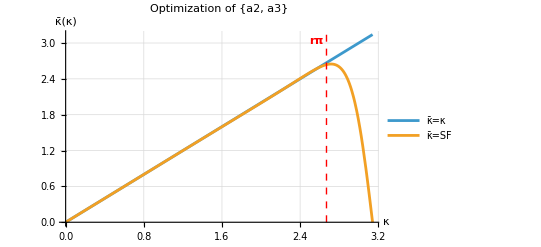

```mathematica
coeffs1={α->0.5674984766667983,β->0.08270928003870921,a1->0.6603882207694884,a2->0.23737572537287543,a3->0.005022695063422676};
r1=2.661/π;
coeffs2={α->0.5698649252859338,β->0.08422366118619422,a1->0.6582794461943285,a2->0.24002829986023835,a3->0.005250846852440635};
r2=2.671/π;
coeffs3={α->0.46212528854158036,β->0.01433680907756551,a1->0.7545208706724549,a2->0.11935743386371474,a3->-0.0055912135935795295};
r3=2.669/π;
coeffs4={α->0.5843384783205174,β->0.09375348681411781,a1->0.6451457202668986,a2->0.2563604647345564,a3->0.00674177179954127};
r4=2.672/π;


(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]
```

```mathematica
Plot[{κ,κBar[κ]/.coeffs1},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a1}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r1*π,0},{r1*π,π}}],Text[Style["rπ",Bold],{r1*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs2},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r2*π,0},{r2*π,π}}],Text[Style["rπ",Bold],{r2*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs3},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{β,a2,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r3*π,0},{r3*π,π}}],Text[Style["rπ",Bold],{r3*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs4},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,β,a3}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r4*π,0},{r4*π,π}}],Text[Style["rπ",Bold],{r4*π-0.1,π-0.1}]}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

# T2 Scheme

## Coefficient Setup

```mathematica
nL=1; (*Number of interior parameters on the LHS*)
nR=2; (*Number of interior parameters on the RHS*)
nF=2; (*Number of free parameters*)
nX=1; (*Number of fixed parameters*)
𝒪=2*(nL+nR-nF); (*Order of accuracy for the scheme*)

(*Choose which parameters are fixed and which are free*)
fixedPars={α};
freePars={a1,a2};

(*Define the fractional wavenumber r*)
r=2.670/π;

(*Optional Kim parameters*)
δ=-0.000240;
n=10;
```

## Solving the System

```mathematica
(*We solve Subscript[n, X] Taylor series equations for the fixed parameters in terms of the free parameters*)
fixedEq1=1+2*α==2*(a1+2*a2);
(*fixedEq2=2/(2!)*α==2/(3!)*(a1+2^3*a2);*)
(*Solve[{fixedEq1,fixedEq2},{α,β}]*)
```

```mathematica
(*We define the numerator, denominator, and spectral function*)
Num[κ_]=2*(a1*Sin[κ]+a2*Sin[2*κ]);
Denom[κ_]=1+2*α*Cos[κ];
κBar[κ_]=Num[κ]/Denom[κ];
```

```mathematica
(*Kim's integrand, Δ^2=(κ-N/D)^2*)
ΔKim22024[κ_]=(κ-Num[κ]/Denom[κ])^2//Together//TrigReduce;
ΔKim2[κ_]=((1+δ)*κ*Denom[κ]-Num[κ])^2*(κ/r)^n;

(*Dr. Hirschmann's integrand, Δ^2=(κD-N)^2*)
ΔDH2[κ_]=(κ*Denom[κ]-Num[κ])^2//Expand;

(*We take the integral of our integrand over κ to arrive at a function for the total error*)
(*ΔKim2[κ]//Expand
ΔDH2[κ]//Expand*)

(*EKim2024=Integrate[ΔKim22024[κ],{κ,0,r*π},Assumptions->{(*0<r<1,*)a1∈Reals,a2∈Reals,a3∈Reals,α∈Reals,β∈Reals}]*)
EKim=Integrate[ΔKim2[κ],{κ,0,r*π},Assumptions->{0<r<=1,n∈Integers,δ∈Reals}];
EDH=Integrate[ΔDH2[κ],{κ,0,r*π},Assumptions->0<r<=1];
```

```mathematica
EDHConstr=EDH/.Solve[fixedEq1,fixedPars[[1]]][[1]]

(*We define Subscript[n, F] new constraint equations for the free parameters to minimize the error*)
freeEq1=D[EDHConstr,freePars[[1]]]==0;
freeEq2=D[EDHConstr,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,freeEq1,freeEq2},{α,a1,a2}][[1]]
coeffs//TableForm//N

freeEq1=D[EKim,freePars[[1]]]==0;
freeEq2=D[EKim,freePars[[2]]]==0;

coeffs=Solve[{fixedEq1,freeEq1,freeEq2},{α,a1,a2}][[1]]
N[coeffs,15]//TableForm
```

6.34472+6.14943 a1^2+5.81531 a2^2-4.85406 (-1+2 a1+4 a2)+2.22291 (-1+2 a1+4 a2)^2+a2 (3.94515-6.16184 (-1+2 a1+4 a2))+a1 (-11.3315+0.500084 a2+1.97257 (-1+2 a1+4 a2))

{α→0.424594,a1→0.779922,a2→0.0723361}

α→0.424594
a1→0.779922
a2→0.0723361

{α→0.438048,a1→0.766067,a2→0.0859903}

α→0.438048
a1→0.766067
a2→0.0859903

## Results

Optimizing over α and a_1 (with r=2.670/π):
	Our results:
		α→0.418231
a1→0.784465
a2→0.0668833
		
		α→0.424594
a1→0.779922
a2→0.0723361
	Kim’s results:
		N/A

Optimizing over α and a_2 (with r=2.670/π):
	Our results:
		α→0.320406
a1→0.896948
a2→-0.0382708
		
		α→0.424594
a1→0.779922
a2→0.0723361
	Kim’s results:
		N/A

Optimizing over a_1 and a_2 (with r=2.670/π):
	Our results:
		α→0.4099
a1→0.787366
a2→0.0612671
		
		α→0.424594
a1→0.779922
a2→0.0723361
	Kim’s results:
		N/A

## r->π

α and a_1:
	α→0.459341
a1→0.770329
a2→0.0945061
	
	α→0.466988
a1→0.757542
a2→0.104723

α and a_2:
	α→0.494872
a1→0.675214
a2→0.159829
	
	α→0.466988
a1→0.757542
a2→0.104723

a_1 and a_2:
	α→0.428571
a1→0.785714
a2→0.0714286
	
	α→0.466988
a1→0.757542
a2→0.104723

## Visualization

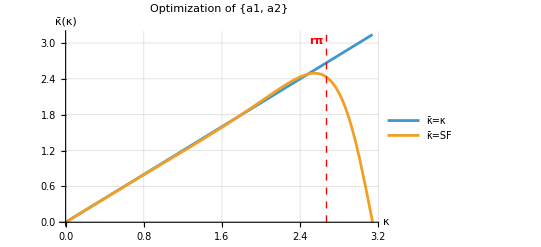

```mathematica
coeffs1={α->0.41823122970441956,a1->0.7844646372810776,a2->0.06688329621167091};
(*coeffs1={α->14/(-9+4 π^2),a1->(4 (-4+π^2))/(-9+4 π^2),a2->-(-51+4 π^2)/(4 (-9+4 π^2))};*)
r1=2.670/π;
coeffs2={α->0.3204064166806459,a1->0.8969479716702151,a2->-0.038270777494784664};
(*coeffs2={α->21/(4 (-19+3 π^2)),a1->-(149-18 π^2)/(4 (-19+3 π^2)),a2->-(3 (-11+π^2))/(2 (-19+3 π^2))};*)
r2=2.670/π;
coeffs3={α->0.40989971396785435,a1->0.7873655261760304,a2->0.061267093895912006};
(*coeffs3={α->3/7,a1->11/14,a2->1/14};*)
r3=2.670/π;

coeffs={α->0.42459428178274977,a1->0.7799221628150456,a2->0.07233605948385209};

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

(*General Plot Code:

Plot[{κ,κBar[κ]/.coeffs},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[freePars],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π}}],Text[Style["rπ",Bold],{r*π-0.1,π-0.1}]}]

*)
```

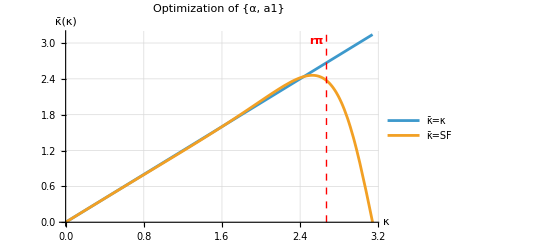

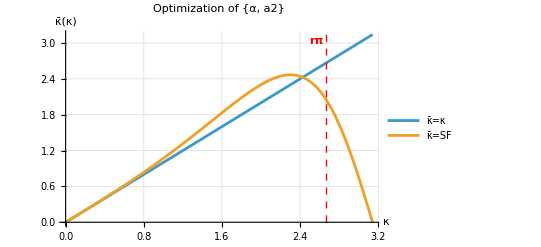

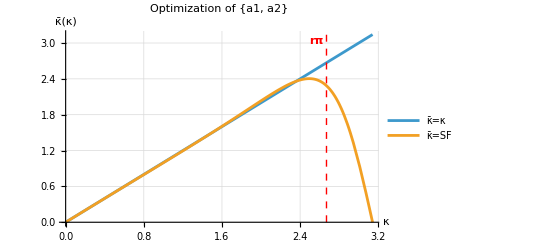

```mathematica
Plot[{κ,κBar[κ]/.coeffs1},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,a1}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r1*π,0},{r1*π,π}}],Text[Style["rπ",Bold],{r1*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs2},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{α,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r2*π,0},{r2*π,π}}],Text[Style["rπ",Bold],{r2*π-0.1,π-0.1}]}]

Plot[{κ,κBar[κ]/.coeffs3},{κ,0,π},PlotRange->{0,π},PlotLabel->"Optimization of "<>ToString[{a1,a2}],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"κ̄=κ","κ̄=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r3*π,0},{r3*π,π}}],Text[Style["rπ",Bold],{r3*π-0.1,π-0.1}]}]
```

## 3D Visualization

```mathematica
EDH3D=EDH/.Solve[fixedEq1,fixedPars[[1]]][[1]]
EDH3DCase1=1/3 π (6 a1^2+π^2+6 a1 (-2+α)-24 α+3 α^2+2 π^2 α^2+1/4 (6-16 α) (1-2 a1+2 α)+3/8 (1-2 a1+2 α)^2);
EDH3DCase2=1/3 π (6 a2^2+π^2+a2 (6-16 α)-24 α+3 α^2+2 π^2 α^2+3 (-2+α) (1-4 a2+2 α)+3/2 (1-4 a2+2 α)^2);
EDH3DCase3=1/3 π (6 a1^2+6 a2^2-12 (-1+2 a1+4 a2)+3/4 (-1+2 a1+4 a2)^2+a2 (6-8 (-1+2 a1+4 a2))+6 a1 (-2+1/2 (-1+2 a1+4 a2))+π^2+1/2 (-1+2 a1+4 a2)^2 π^2);
(*Plot3D[EDH3D,{a1,-1,1},{α,-1,1}]*)


Plot3D[EDH3DCase1,{a1,-1,1},{α,-1,1}]
Plot3D[EDH3DCase2,{a2,-1,1},{α,-1,1}]
Plot3D[EDH3DCase3,{a1,-1,1},{a2,-1,1}]
```

1/3 π (6 a1^2+6 a2^2-12 (-1+2 a1+4 a2)+3/4 (-1+2 a1+4 a2)^2+a2 (6-8 (-1+2 a1+4 a2))+6 a1 (-2+1/2 (-1+2 a1+4 a2))+π^2+1/2 (-1+2 a1+4 a2)^2 π^2)

-Graphics3D-

-Graphics3D-

-Graphics3D-